# Examen parcial II

## Ejercicio I:

Clasifica las bifurcaciones de los siguientes sistemas, calcula el valor crítico  en el cual ocurre la bifurcación y grafica el diagrama de bifurcación

Los primeros tres incisos son fáciles calculando los puntos de equilibrio. Empezamos por ver que, de inmediato, el lado izquierdo de la ecuación es cero cuando , por lo que siempre existe el punto de equilibrio . Ahora igualamos el lado derecho de la igualdad a cero y dividimos entre  para encontrar los demás puntos de equilibrio:

Multiplicando por  de ambos lados:

Expandiendo y dividiendo entre :

Despejando:

Vemos que todos los puntos de equilibrio son iguales cuando  y cuando  sólo existe la solución de equilibrio , por lo que debe ser una bifurcación de tridente con . Para determinar si es supercrítica o subcrítica, basta con calcular si la solución de equilibrio que siempre existe es estable cuando existen o no existen las otras dos soluciones. Derivamos el lado derecho de la ecuación:

Evaluamos en :

Vemos que  cuando , por lo que es estable en este rango, y similarmente, es inestable cuando . La solución cero es estable cuando los otros dos puntos de equilibrio existen e inestable cuando sólo ella existe, por lo que es una bifurcación de tridente subcrítica. Usando esta información podemos graficar el diagrama:

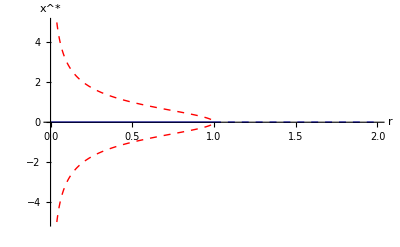

```mathematica
Show[Plot[0,{r,0,1},PlotStyle->{Blue,Thick},AxesLabel->{r,SuperStar[x]},PlotRange->{{0,2},{-5,5}}],Plot[0,{r,1,2},PlotStyle->{Blue,Thick,Dashed}],Plot[Sqrt[1/r-1],{r,1/26,1},PlotStyle->{Red,Dashed,Thick}],Plot[-Sqrt[1/r-1],{r,1/26,1},PlotStyle->{Red,Dashed,Thick}]]
```

Procediendo de la misma forma que en el caso anterior, vemos que  siempre  es una solución de equilibrio. Calculando su estabilidad:

Evaluando:

Igual que en el caso anterior, esta solución de equilibrio es estable cuando  e inestable cuando , por lo que la bifurcación ocurre cuando . Calculamos otros puntos de equilibrio igual que antes





Vemos que el punto de equilibrio  existe siempre que  y en   lo que confirma que . Como en este punto uno de los puntos de equilibrio cambia de estabilidad, pero el otro no deja de existir, concluimos que debe ser una bifurcación transcrítica. Lo comprobamos mediante el diagrama de bifurcación (no es necesario calcular la estabilidad del segundo punto de equilibrio, ya que el cero cambia de estabilidad cuando colisionan, podemos estar seguros que el otro intercambia estabilidad).

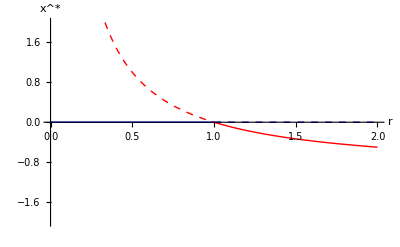

```mathematica
Show[Plot[0,{r,0,1},PlotStyle->{Blue,Thick},PlotRange->{{0,2},{-2,2}},AxesLabel->{r,SuperStar[x]}],Plot[0,{r,1,2},PlotStyle->{Blue,Thick,Dashed}],Plot[1/r-1,{r,1/3,1},PlotStyle->{Red,Dashed,Thick}],Plot[1/r-1,{r,1,2},PlotStyle->{Red,Thick}]]
```

Aquí también  y para calcular su estabilidad evaluamos , , por lo que la solución es estable cuando  e inestable cuando . Podemos intuir que . Calculando los otros puntos de equilibrio:





Vemos que, cuando , los tres puntos de equilibrio son iguales. Los últimos dos puntos de equilibrio existen cuando  es decir, cuando . Esto quiere decir que la bifurcación es de tridente supercrítica cuando pues la única solución de equilibrio estable se divide en una solución de equilibrio inestable y dos estables.
Con esto ya podemos dibujar el diagrama de bifurcación:

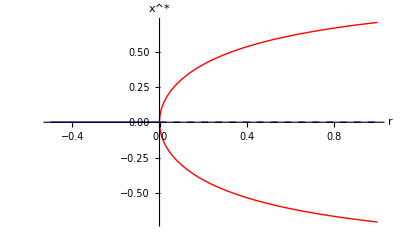

```mathematica
Show[Plot[0,{r,-1/2,0},PlotStyle->{Blue,Thick},AxesLabel->{r,SuperStar[x]},PlotRange->{{-1/2,1},{-Sqrt[1/2],Sqrt[1/2]}}],Plot[0,{r,0,1},PlotStyle->{Blue,Thick,Dashed}],Plot[Sqrt[r/(r+1)],{r,0,1},PlotStyle->{Red,Thick}],Plot[-Sqrt[r/(r+1)],{r,0,1},PlotStyle->{Red,Thick}]]
```

Aquí conviene una estrategia un poco diferente. Vemos que si , entonces el lado derecho de la igualdad es , por lo que  es una solución de equilibrio si . Como ya identificamos un punto de equilibrio que podría estar involucrado en la bifurcación, podemos expandir en series de Taylor alrededor de ese valor, donde necesitamos las derivadas de . Lo haremos hasta segundo orden en caso de que la bifurcación sea nodo-silla o transcrítica. Podemos hacer esto de manera numérica o a mano:

```mathematica
Series[Exp[-x^2],{x,0,2}]
```

1-x^2+O[x]^3

Sustituimos en la ecuación:

Distribuimos el producto 

Multiplicamos de ambos lados por  y usamos la linealidad de la derivada:

Hacemos el cambio de variable :

Finalmente, definimos 

la cual es la forma normal de la bifurcación de nodo silla. La bifurcación ocurre cuando , es decir, cuando  (este es el punto donde la  alrededor de donde estamos expandiendo es solución). Para las estabilidades a la hora de dibujar el diagrama de bifurcación, conviene saber de qué lado es estable y de qué lado es inestable el punto de equilibrio en la bifurcación, ya que los puntos de equilibrio después de la bifurcación heredan esta antisimetría en estabilidad. Cuando , podemos reescribir la ecuación de la forma: . Ahora, sabemos que la función , donde la igualdad se da en . Esto quiere decir que , por lo que , es decir, todas las soluciones son no decrecientes. Como  es una solución de equilibrio, esto quiere decir que las soluciones se acercan al equilibrio por la izquierda y se alejan por la derecha. De igual forma, después de la bifurcación, el menor de los puntos de equilibrio es estable y el mayor es inestable.
El diagrama de bifurcación en este caso es numérico, y se puede encontrar como:

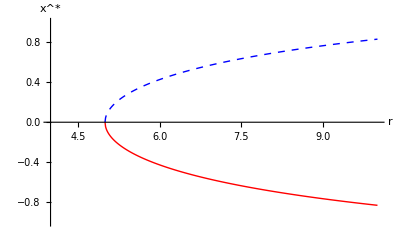

```mathematica
branch1=ParallelTable[{r,x/.FindRoot[5-r*Exp[-x^2]==0,{x,-1}]},{r,5,10,0.01}];
branch2=ParallelTable[{r,x/.FindRoot[5-r*Exp[-x^2]==0,{x,1}]},{r,5,10,0.01}];
Show[ListPlot[branch1,AxesLabel->{r,SuperStar[x]},Joined->True,PlotStyle->{Red,Thick},PlotRange->{{4,10},{-1,1}}],ListPlot[branch2,Joined->True,PlotStyle->{Blue,Thick,Dashed}]]
```

## Ejercicio II:

La aproximación a tercer orden de un modelo real que describe el ordenamiento autoorganizado de un cristal líquido está dada por

donde  es llamado el director nemático,  es el tiempo, y ,  y  son parámetros.

Si  tiene unidades de tiempo y  tiene unidades de densidad, y la ecuación es dimensionalmente correcta, ¿cuáles son las unidades de  y ?

Como  es el límite de una división de incrementos de  entre incrementos de , ésta debe tener unidades de  entre tiempo. Como la ecuación es dimensionalmente correcta, el lado derecho de la igualdad tambipen tiene unidades de  entre tiempo. Vemos que  también tiene unidades de  entre tiempo, dadas las unidades de . Esto quiere decir que el factor que está multiplicando a  no debe tener unidades. Ahora, el paréntesis más interno tiene a un número (sin unidades) restando a . Para que esto sea correcto, se necesita que  tampoco tenga unidades, por lo que las unidades de  y de  deben ser recíprocos. Finalmente, como acabamos de discutir, el paréntesis interno no tiene unidades, por lo que al multiplicar por , todo esto tiene unidades de , pero como ya habíamos discutido, todo lo del paréntesis externo tampoco debe tener unidades (esto también se puede ver porque hay un  restando que no tiene unidades), por lo que  y  también deben tener unidades recíprocas. Como  tiene unidades de densidad, entonces  tiene unidades de densidad, por lo que  tiene unidades de densidad.

Encuentra la solución de equilibrio trivial de la ecuación, y determina su estabilidad. ¿Cuál debería ser el punto donde ocurre la bifurcación?

Vemos que cuando , el lado derecha de la ecuación es cero, por lo que la solución de equilibrio trivial es . Para determinar su estabilidad derivamos el lado derecho de la igualdad respecto de  y evaluamos en la solución de equilibrio:


El eigenvalor cambia de signo cuando , por lo que en este punto debería ocurrir la bifurcación

Determina el tipo de bifurcación que ocurre y lleva la ecuación a su forma normal. Suponiendo que los tres parámetros son estrictamente positivos. ¿Cuáles son los parámetros bifurcantes? Pista: No todos los parámetros juegan un papel en la bifurcación en este caso.

Como vimos, hay una solución de equilibrio que siempre existe, por lo que no puede ser una bifurcación de nodo-silla. Además, la forma polinomial del lado derecho es cúbica, lo que sugiera que es una bifurcación de tridente. Expandimos el lado derecho de la ecuación diferencial:

vemos que el término cúbico es negativo, por lo que debe ser una bifurcación de tridente supercrítica. Empezamos por distribuir la  dentro del paréntesis:

Ahora ponemos las constantes dentro del término cuadrático:

Multiplicamos toda la ecuación por la raíz, y usamos la linealidad de la derivada:

Hacemos el cambio de variable :

Definimos :

Distribuimos el producto:

La cual es la forma normal. Ahora, la bifurcación se da en . Usando la definición de  vemos que la bifurcación se da cuando

Como  es estrictamente positivo, podemos dividir de ambos lados y obtenemos la misma condición que antes:
. Vemos que  no participa en la bifurcación, por lo que  y  son los únicos parámetros bifurcantes.